```mathematica
Clear["`*"]
```

## Hide this (T8 with 7th order on Boundary)

```mathematica
alpha=3.0/8.0;
a1=25.0/16.0;
a2=1.0/5.0;
a3=-1.0/80.0;
gamma01=3.210113927329531;
gamma10=2.21110473043239;
gamma12=42.08319933908019;
gamma21=1.557633196122124;
gamma23=6.482610425055064;
gamma32=-1.329341564172446;
gamma34=-2.465569273620743;
gamma43=-1.213703810247279;
gamma45=1.660769542489766;
gamma54=-0.1776191023391513;
gamma56=0.2232924886469337;
a00=-3.051444846761362;
a01=2.345334805372179;
a02=-0.8696582180114061;
a03=3.641381848342838;
a04=-3.399810121117448;
a05=1.792414554502852;
a06=-0.5246438812007604;
a07=0.0664258588731064;
a10=-4.873954900119216;
a12=-53.18177248515291;
a13=93.4348874201782;
a14=-52.74983250718357;
a15=22.56437298084277;
a16=-5.886555463761137;
a17=0.692854955195867;
a20=-0.2604486511132088;
a21=-1.943640425204907;
a23=-3.84806892990241;
a24=8.245332418591937;
a25=-2.779674691274779;
a26=0.6603673342280958;
a27=-0.0738670553247296;
a30=-0.05878600824425402;
a31=0.7074851396321982;
a32=-0.2983532234844736;
a34=1.491392318405186;
a35=-2.222455418896595;
a36=0.4240020577097782;
a37=-0.0432848651218399;
a40=0.05619441751764617;
a41=-0.4761142198435586;
a42=1.967293657743868;
a43=-2.297921866880887;
a45=-0.7202751534930111;
a46=1.865337479238859;
a47=-0.447823643536206;
a48=0.0533093292532889;
a50=-0.005353093751500729;
a51=0.04953262252336028;
a52=-0.2157074945553577;
a53=0.6319138819385537;
a54=-1.144234713147819;
a56=0.6783115550998231;
a57=0.005414306071706973;
a58=0.0001229358212328832;
```

```mathematica
(*Create and display a tridiagonal matrix with 3 boundary rows*)
triRowsLHS[i_,j_,D_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=6;
(*If[(i==1&&j==1)||(i==k&&j==k),gamma00,
If[(i==1&&j==2)||(i==k&&j==k-1),gamma01,*)
(*If[(i-1==j)&&(i<=numBoundaryRows||k-i>=numBoundaryRows),gamma[i-1,j-1]]*)
If[(i-1==j)&&(i<=numBoundaryRows),ToExpression["gamma"<>ToString[i-1]<>ToString[j-1]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["gamma"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(i<=numBoundaryRows),ToExpression["gamma"<>ToString[i-1]<>ToString[j-1]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["gamma"<>ToString[k-i]<>ToString[k-j]],

If[i-1==j, alpha,
If[i==j, 1,
If[i+1==j, alpha,
0]]]]]]]]
BoundTriMatrixLHS[D_,k_]:=Array[triRowsLHS[#1,#2,D,k]&,{k,k}]

LHS[k_]=BoundTriMatrixLHS[d,k];
LHS[20]//MatrixForm
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[triRowsLHS[#1,#2,d,k]&,{k,k}].

(1 | 3.21011 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2111 | 1 | 42.0832 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.55763 | 1 | 6.48261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1.32934 | 1 | -2.46557 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.2137 | 1 | 1.66077 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.177619 | 1 | 0.223292 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.375 | 1 | 0.375 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.223292 | 1 | -0.177619 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66077 | 1 | -1.2137 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.46557 | 1 | -1.32934 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.48261 | 1 | 1.55763 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42.0832 | 1 | 2.2111
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.21011 | 1)

```mathematica
(*Create and display a tridiagonal matrix with 3 boundary rows*)
triRowsRHS[i_,j_,D_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==1,a00,
If[i==1&&j==2,a01,
If[i==1&&j==3,a02,
If[i==1&&j==4,a03,
If[i==1&&j==5,a04,
If[i==1&&j==6,a05,
If[i==1&&j==7,a06,
If[i==1&&j==8,a07,

If[i==2&&j==1,a10,
If[i==2&&j==3,a12,
If[i==2&&j==4,a13,
If[i==2&&j==5,a14,
If[i==2&&j==6,a15,
If[i==2&&j==7,a16,
If[i==2&&j==8,a17,

If[i==3&&j==1,a20,
If[i==3&&j==2,a21,
If[i==3&&j==4,a23,
If[i==3&&j==5,a24,
If[i==3&&j==6,a25,
If[i==3&&j==7,a26,
If[i==3&&j==8,a27,

If[i==4&&j==1,a30,
If[i==4&&j==2,a31,
If[i==4&&j==3,a32,
If[i==4&&j==5,a34,
If[i==4&&j==6,a35,
If[i==4&&j==7,a36,
If[i==4&&j==8,a37,

If[i==5&&j==1,a40,
If[i==5&&j==2,a41,
If[i==5&&j==3,a42,
If[i==5&&j==4,a43,
If[i==5&&j==6,a45,
If[i==5&&j==7,a46,
If[i==5&&j==8,a47,
If[i==5&&j==9,a48,

If[i==6&&j==1,a50,
If[i==6&&j==2,a51,
If[i==6&&j==3,a52,
If[i==6&&j==4,a53,
If[i==6&&j==5,a54,
If[i==6&&j==7,a56,
If[i==6&&j==8,a57,
If[i==6&&j==9,a58,



If[i==k&&j==k,-a00,
If[i==k&&j==k-1,-a01,
If[i==k&&j==k-2,-a02,
If[i==k&&j==k-3,-a03,
If[i==k&&j==k-4,-a04,
If[i==k&&j==k-5,-a05,
If[i==k&&j==k-6,-a06,
If[i==k&&j==k-7,-a07,

If[i==k-1&&j==k,-a10,
If[i==k-1&&j==k-2,-a12,
If[i==k-1&&j==k-3,-a13,
If[i==k-1&&j==k-4,-a14,
If[i==k-1&&j==k-5,-a15,
If[i==k-1&&j==k-6,-a16,
If[i==k-1&&j==k-7,-a17,

If[i==k-2&&j==k,-a20,
If[i==k-2&&j==k-1,-a21,
If[i==k-2&&j==k-3,-a23,
If[i==k-2&&j==k-4,-a24,
If[i==k-2&&j==k-5,-a25,
If[i==k-2&&j==k-6,-a26,
If[i==k-2&&j==k-7,-a27,

If[i==k-3&&j==k,-a30,
If[i==k-3&&j==k-1,-a31,
If[i==k-3&&j==k-2,-a32,
If[i==k-3&&j==k-4,-a34,
If[i==k-3&&j==k-5,-a35,
If[i==k-3&&j==k-6,-a36,
If[i==k-3&&j==k-7,-a37,

If[i==k-4&&j==k,-a40,
If[i==k-4&&j==k-1,-a41,
If[i==k-4&&j==k-2,-a42,
If[i==k-4&&j==k-3,-a43,
If[i==k-4&&j==k-5,-a45,
If[i==k-4&&j==k-6,-a46,
If[i==k-4&&j==k-7,-a47,
If[i==k-4&&j==k-8,-a48,

If[i==k-5&&j==k,-a50,
If[i==k-5&&j==k-1,-a51,
If[i==k-5&&j==k-2,-a52,
If[i==k-5&&j==k-3,-a53,
If[i==k-5&&j==k-4,-a54,
If[i==k-5&&j==k-6,-a56,
If[i==k-5&&j==k-7,-a57,
If[i==k-5&&j==k-8,-a58,



If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
BoundTriMatrixRHS[D_,k_]:=Array[triRowsRHS[#1,#2,D,k]&,{k,k}]

RHS[k_]=BoundTriMatrixRHS[d,k];
RHS[20]//MatrixForm
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[triRowsRHS[#1,#2,d,k]&,{k,k}].

(-3.05144 | 2.34533 | -0.869658 | 3.64138 | -3.39981 | 1.79241 | -0.524644 | 0.0664259 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.87395 | 0 | -53.1818 | 93.4349 | -52.7498 | 22.5644 | -5.88656 | 0.692855 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.260449 | -1.94364 | 0 | -3.84807 | 8.24533 | -2.77967 | 0.660367 | -0.0738671 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.058786 | 0.707485 | -0.298353 | 0 | 1.49139 | -2.22246 | 0.424002 | -0.0432849 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0561944 | -0.476114 | 1.96729 | -2.29792 | 0 | -0.720275 | 1.86534 | -0.447824 | 0.0533093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00535309 | 0.0495326 | -0.215707 | 0.631914 | -1.14423 | 0 | 0.678312 | 0.00541431 | 0.000122936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0125 | -0.2 | -1.5625 | 0 | 1.5625 | 0.2 | -0.0125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000122936 | -0.00541431 | -0.678312 | 0 | 1.14423 | -0.631914 | 0.215707 | -0.0495326 | 0.00535309
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0533093 | 0.447824 | -1.86534 | 0.720275 | 0 | 2.29792 | -1.96729 | 0.476114 | -0.0561944
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0432849 | -0.424002 | 2.22246 | -1.49139 | 0 | 0.298353 | -0.707485 | 0.058786
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0738671 | -0.660367 | 2.77967 | -8.24533 | 3.84807 | 0 | 1.94364 | 0.260449
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.692855 | 5.88656 | -22.5644 | 52.7498 | -93.4349 | 53.1818 | 0 | 4.87395
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0664259 | 0.524644 | -1.79241 | 3.39981 | -3.64138 | 0.869658 | -2.34533 | 3.05144)

## Run this

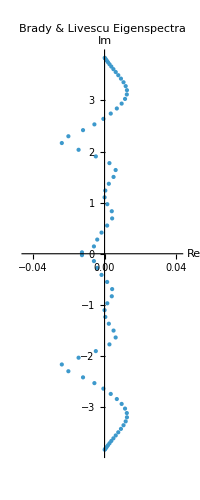

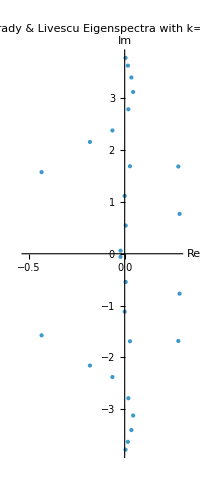

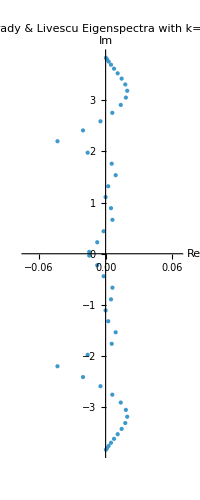

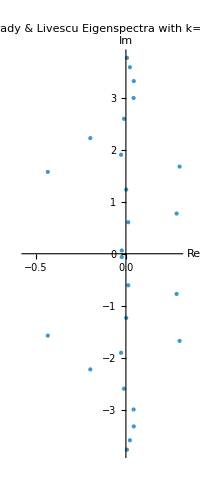

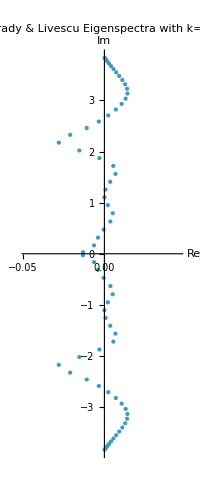

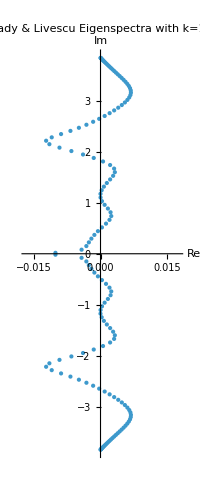

```mathematica
h=1;
(*k=160;*)
size=92;

characteristicPolynomial[λ_]=Det[Inverse[LHS[size]]]*Det[RHS[size]-λ*h*LHS[size]]
(*Plot[characteristicPolynomial[λ],{λ,-20,20}]*)
eig[k_]:=Module[{LHSMat,RHSMat},
LHSMat=Inverse[Transpose[Drop[Transpose[Drop[LHS[k],1]],1]]];
RHSMat=Transpose[Drop[Transpose[Drop[RHS[k],1]],1]];
Eigenvalues[-LHSMat.RHSMat]*h
];
ComplexListPlot[eig[size],PlotLabel->"Brady & Livescu Eigenspectra",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[32],PlotLabel->"Brady & Livescu Eigenspectra with k=16",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[62],PlotLabel->"Brady & Livescu Eigenspectra with k=28",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[30],PlotLabel->"Brady & Livescu Eigenspectra with k=29",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[82],PlotLabel->"Brady & Livescu Eigenspectra with k=80",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[162],PlotLabel->"Brady & Livescu Eigenspectra with k=160",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
```